# Data generation

Artificial data generation for clulstering varidity.

Data structire:
<Model and annotation>
;
<Dimension>[\tab]<Number of clusters>[\tab]<Number of samples>[\tab]<Number of background points>
;
<Cluster centers (model): matrix with tab delimiter>
;
<Samples: matrix with tab delimiter>
;

## Preparation

```mathematica
Get["/Users/amanokou/SCRIPT-MATHEMATICA/SCRIPTS/polar.txt"]
```

```mathematica
SetDirectory["/Users/amanokou/gitsrc/ClusteringAdequation"]
```

/Users/amanokou/gitsrc/ClusteringAdequation

## Programs

```mathematica
strDataToExportStr[n_]:=StringJoin[Riffle[{anntS[n],dimS[n],centersS[n],samplesS[n]},";\n"]]
```

```mathematica
distanceMat[mat_]:=Module[
{n},
n=Length[mat];
Table[EuclideanDistance[mat[[i]],mat[[j]]],{i,n},{j,n}]
]
```

## 2D

### data 1 (general)

```mathematica
anntS[1]="Model: central random, circles, one radius, triangle.\n"
```

Model: central random, circles, one radius, triangle.

```mathematica
dim[1]=2;
numClass[1]=3;
numSample[1]={100,100,100};
numBG[1]={0};
```

```mathematica
dimS[1]=StringJoin[Riffle[{ToString[dim[1]],ToString[numClass[1]],ToString[numSample[1]],ToString[numBG[1]]},"\t"],"\n"]
```

2	3	{100, 100, 100}	{0}

```mathematica
centers[1]=Map[polarToxy[N[{1,#}]]&,Table[2Pi/numClass[1] n,{n,0,2}]]
```

{{1.,0.},{-0.5,0.866025},{-0.5,-0.866025}}

```mathematica
centersS[1]=ExportString[centers[1],"TSV"]<>"\n"
```

1.	0.
-0.4999999999999998	0.8660254037844388
-0.5000000000000004	-0.8660254037844384

```mathematica
distanceMat[centers[1]]
```

{{0.,1.73205,1.73205},{1.73205,0.,1.73205},{1.73205,1.73205,0.}}

```mathematica
distMean[1]=Tr[Flatten[distanceMat[centers[1]]]]/(numClass[1]^2-numClass[1])
```

1.73205

```mathematica
samples[1]=Table[Map[#+centers[1][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[1]/2}],RandomReal[{0,2Pi}]}],{numSample[1][[n]]}]],{n,numClass[1]}];
```

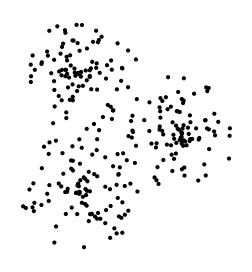

```mathematica
Graphics[Map[Point[#]&,samples[1],{2}]]
```

```mathematica
samplesS[1]=ExportString[Flatten[samples[1],1],"TSV"]<>"\n";
```

```mathematica
(*Export["data1.tsv",strDataToExportStr[1],"String"]*)
```

data1.tsv

### data 2 (unbalanced)

```mathematica
anntS[2]="Model: unbalanced central random, circles, radiuses.\n"
```

Model: unbalanced central random, circles, radiuses.

```mathematica
dim[2]=2;
numClass[2]=3;
numSample[2]={200,100,50};
numBG[2]={0};
```

```mathematica
dimS[2]=StringJoin[Riffle[{ToString[dim[2]],ToString[numClass[2]],ToString[numSample[2]],ToString[numBG[2]]},"\t"],"\n"]
```

2	3	{200, 100, 50}	{0}

```mathematica
centers[2]={{0,0},{0.5,-1},{-0.5,-0.75}}
```

{{0,0},{0.5,-1},{-0.5,-0.75}}

```mathematica
centersS[2]=ExportString[centers[2],"TSV"]<>"\n"
```

0	0
0.5	-1
-0.5	-0.75

```mathematica
distanceMat[centers[2]]
```

{{0,1.11803,0.901388},{1.11803,0.,1.03078},{0.901388,1.03078,0.}}

```mathematica
distMean[2]=Tr[Flatten[distanceMat[centers[2]]]]/(numClass[2]^2-numClass[2])
```

1.01673

```mathematica
radius[2]={distMean[2]*0.6,distMean[2]*0.4,distMean[2]*0.2}
```

{0.61004,0.406693,0.203347}

```mathematica
samples[2]=Table[Map[#+centers[2][[n]]&,Table[polarToxy[{RandomReal[{0,radius[2][[n]]}],RandomReal[{0,2Pi}]}],{numSample[2][[n]]}]],{n,numClass[2]}];
```

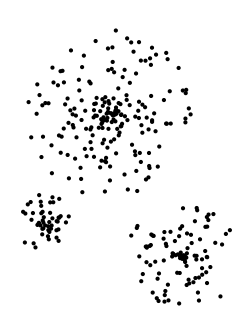

```mathematica
Graphics[Map[Point[#]&,samples[2],{2}]]
```

```mathematica
samplesS[2]=ExportString[Flatten[samples[2],1],"TSV"]<>"\n";
```

```mathematica
(*Export["data2.tsv",strDataToExportStr[2],"String"]*)
```

data2.tsv

### data 3 (noisy)

```mathematica
anntS[3]="Model: central random + noise, circles, one radius, triangle.\n"
```

Model: central random + noise, circles, one radius, triangle.

```mathematica
dim[3]=2;
numClass[3]=3;
numSample[3]={100,100,100};
numBG[3]={100};
```

```mathematica
dimS[3]=StringJoin[Riffle[{ToString[dim[3]],ToString[numClass[3]],ToString[numSample[3]],ToString[numBG[3]]},"\t"],"\n"]
```

2	3	{100, 100, 100}	{100}

```mathematica
centers[3]=Map[polarToxy[N[{1,#}]]&,Table[2Pi/numClass[3] n,{n,0,2}]]
```

{{1.,0.},{-0.5,0.866025},{-0.5,-0.866025}}

```mathematica
centersS[3]=ExportString[centers[3],"TSV"]<>"\n"
```

1.	0.
-0.4999999999999998	0.8660254037844388
-0.5000000000000004	-0.8660254037844384

```mathematica
distanceMat[centers[3]]
```

{{0.,1.73205,1.73205},{1.73205,0.,1.73205},{1.73205,1.73205,0.}}

```mathematica
distMean[3]=Tr[Flatten[distanceMat[centers[3]]]]/(numClass[3]^2-numClass[3])
```

1.73205

```mathematica
samples[3,"class"]=Table[Map[#+centers[3][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[3]/2}],RandomReal[{0,2Pi}]}],{numSample[3][[n]]}]],{n,numClass[3]}];
```

```mathematica
maxmin[3]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[3,"class"],1]]]
```

{{1.79368,-1.31631},{1.71724,-1.68456}}

```mathematica
samples[3,"background"]=Table[{RandomReal[maxmin[3][[1]]],RandomReal[maxmin[3][[2]]]},{numBG[3][[1]]}];
```

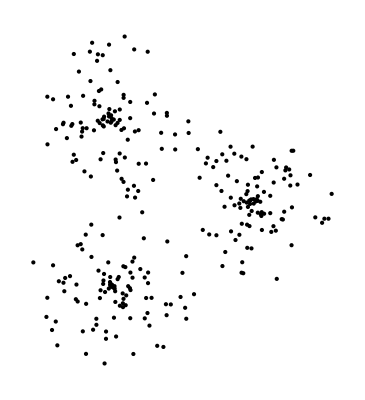

```mathematica
Graphics[Map[Point[#]&,Flatten[samples[3,"class"],1]]]
```

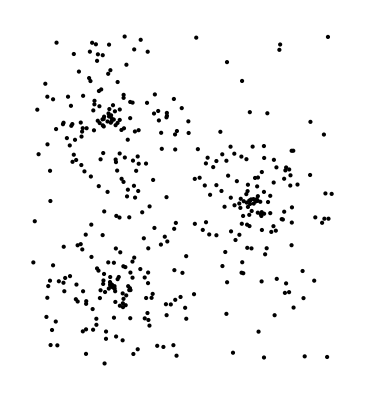

```mathematica
Graphics[Map[Point[#]&,Join[Flatten[samples[3,"class"],1],samples[3,"background"]]]]
```

```mathematica
samplesS[3]=ExportString[Join[Flatten[samples[3,"class"],1],samples[3,"background"]],"TSV"]<>"\n";
```

```mathematica
(*Export["data3.tsv",strDataToExportStr[3],"String"]*)
```

data3.tsv

## 3D

## high Dimensional

## Experimental

```mathematica
Map[polarToxy[{1,#}]&,Table[2Pi/3 n,{n,0,2}]]
```

{{1,0},{-1/2,(√3)/2},{-1/2,-(√3)/2}}

```mathematica
Graphics[Map[Point[#]&,Map[polarToxy[{1,#}]&,Table[2Pi/3 n,{n,0,2}]]]]
```

-Graphics-